```mathematica
(*Початоква купа формул*)
ClearAll[x,t]
G:=(-Log[x^2+t^2]/Pi)/.{x->(x-xI),t->(t-tI)}
G:=(x^2+t^2)/.{x->(x-xI),t->(t-tI)}
G
u := -1/5*Sin[x/5]-1/4*Cos[t/4]
uI:=u/.{x->xI,t->tI}
y:=5x+4t
(*Просторово-часова область*)
t1:=0
t2:=50
x1:=0
x2:=50
T:={t,t1,t2}
TI:=T/.{t->tI}
X:={x,x1,x2}
XI:=X/.{x->xI}
```

(t-tI)^2+(x-xI)^2

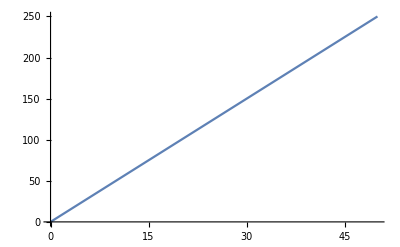

```mathematica
(*Початкові умови*)
Plot[y/.{t->t1},Evaluate[X]]
```

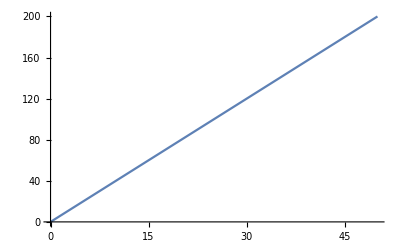

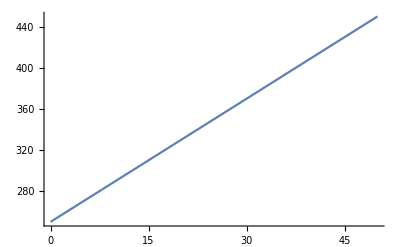

```mathematica
(*Крайові умови*)
Plot[y/.{x->x1},Evaluate[T]]
Plot[y/.{x->x2},Evaluate[T]]
```

```mathematica
(*Перший у*)
(*yInf=Re[N[Integrate[G*u,Evaluate[X],Evaluate[T]]]]*)
yInf:=Integrate[G*uI,Evaluate[XI],Evaluate[TI]]
yInf
```

50/3 (-2350+126 t-3 t^2-3 x^2+(9850+3 (-50+t) t+3 (-100+x) x) Cos[10]+24 (-50+t) Cos[25/2]+30 (-50+x) Sin[10]+(-9904-3 (-100+t) t-3 (-50+x) x) Sin[25/2])

```mathematica
(*Точки для подбудови вектори U*)
(*m0:={{xI->1,tI->-10},{xI->2,tI->-20},{xI->3,tI->-30},{xI->4,tI->-1},{xI->5,tI->-2}}
mE:={{xI->100,tI->1},{xI->200,tI->30},{xI->55,tI->10},{xI->65,tI->20},{xI->75,tI->30}}*)
m0:={{xI->1,tI->-10},{xI->2,tI->-20}}
mE:={{xI->100,tI->1},{xI->200,tI->30}}
(*Вектори В*)
B11:=G/.m0
B12:=G/.mE
B21:=G/.m0
B22:=G/.mE
B:={Join[B11,B12],Join[B21,B22]}
Y:={y*Boole[t==0&&x≠(x2-x1)],y*Boole[x==(x2-x1)&&t≠0]}
B//MatrixForm
Transpose[B]//MatrixForm
Y/.{x->5,t->0}
(Transpose[B].Y)[[1]]
(Transpose[B].Y)[[1]]/.{t->0}
```

((10+t)^2+(-1+x)^2 | (20+t)^2+(-2+x)^2 | (-1+t)^2+(-100+x)^2 | (-30+t)^2+(-200+x)^2
(10+t)^2+(-1+x)^2 | (20+t)^2+(-2+x)^2 | (-1+t)^2+(-100+x)^2 | (-30+t)^2+(-200+x)^2)

((10+t)^2+(-1+x)^2 | (10+t)^2+(-1+x)^2
(20+t)^2+(-2+x)^2 | (20+t)^2+(-2+x)^2
(-1+t)^2+(-100+x)^2 | (-1+t)^2+(-100+x)^2
(-30+t)^2+(-200+x)^2 | (-30+t)^2+(-200+x)^2)

{25,0}

((10+t)^2+(-1+x)^2) (4 t+5 x) Boole[t==0&&x≠50]+((10+t)^2+(-1+x)^2) (4 t+5 x) Boole[x==50&&t≠0]

5 (100+(-1+x)^2) x Boole[x≠50]

```mathematica
By2:=Integrate[(Transpose[B].Y)/.{t->0},Evaluate[X]]+Integrate[(Transpose[B].Y)/.{x->(x2-x1)},Evaluate[T]]
By2
```

{234133750/3,92657500,264383750/3,1732562500/3}

```mathematica
By:=Integrate[(B[[1]]*y)/.{t->0},Evaluate[X]]+Integrate[(B[[2]]*y)/.{x->(x2-x1)},Evaluate[T]]
By2-By
```

{0,0,0,0}

```mathematica
Transpose[B].B
```

{{2 ((10+t)^2+(-1+x)^2)^2,2 ((20+t)^2+(-2+x)^2) ((10+t)^2+(-1+x)^2),2 ((-1+t)^2+(-100+x)^2) ((10+t)^2+(-1+x)^2),2 ((-30+t)^2+(-200+x)^2) ((10+t)^2+(-1+x)^2)},{2 ((20+t)^2+(-2+x)^2) ((10+t)^2+(-1+x)^2),2 ((20+t)^2+(-2+x)^2)^2,2 ((-1+t)^2+(-100+x)^2) ((20+t)^2+(-2+x)^2),2 ((-30+t)^2+(-200+x)^2) ((20+t)^2+(-2+x)^2)},{2 ((-1+t)^2+(-100+x)^2) ((10+t)^2+(-1+x)^2),2 ((-1+t)^2+(-100+x)^2) ((20+t)^2+(-2+x)^2),2 ((-1+t)^2+(-100+x)^2)^2,2 ((-30+t)^2+(-200+x)^2) ((-1+t)^2+(-100+x)^2)},{2 ((-30+t)^2+(-200+x)^2) ((10+t)^2+(-1+x)^2),2 ((-30+t)^2+(-200+x)^2) ((20+t)^2+(-2+x)^2),2 ((-30+t)^2+(-200+x)^2) ((-1+t)^2+(-100+x)^2),2 ((-30+t)^2+(-200+x)^2)^2}}

```mathematica
(*Вектори Ву*)
(*By1:=Integrate[B11.y/.{t->0},Evaluate[X]]+Total[Integrate[B21.y,Evaluate[T]]/.{x->{x2-x1}}][[1]]
By2:=Total[Integrate[B12*y/.{t->0},Evaluate[X]]][[1]]+Total[Integrate[B22*y,Evaluate[T]]/.{x->{x2-x1}}][[1]]
Transpose[B11]
Integrate[B11.y/.{t->0},Evaluate[X]]*)
```

```mathematica
(*Р2*)
(*P11:=Total[Integrate[B11^2,Evaluate[X]]]+Total[Integrate[B21^2,Evaluate[T]]/.{x->{x2-x1}}][[1]]
P12:=Total[Integrate[B11*B12,Evaluate[X]]]+Total[Integrate[B21*B22,Evaluate[T]]/.{x->{x2-x1}}][[1]]
P21:=Total[Integrate[B12*B11,Evaluate[X]]]+Total[Integrate[B22*B21,Evaluate[T]]/.{x->{x2-x1}}][[1]]
P22:=Total[Integrate[B12^2,Evaluate[X]]]+Total[Integrate[B22^2,Evaluate[T]]/.{x->{x2-x1}}][[1]]*)
```

```mathematica
(*u0*)
u0:=P11*By1+P12*By2
uE:=P21*By1+P22*By2
```